```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=40;
```

```mathematica
Manipulate[
data=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt","Table"];
dataX=Select[data,#[[3]]=="X"&][[;;,{1,2}]];
dataY=Select[data,#[[3]]=="Y"&][[;;,{1,2}]];
dataX2=ConstantArray[0,{boxLength,boxLength}];
dataY2=ConstantArray[0,{boxLength,boxLength}];
Do[
dataX2[[pt[[1]],pt[[2]]]]=1;
,{pt,dataX}];
Do[
dataY2[[pt[[1]],pt[[2]]]]=1;
,{pt,dataY}];
ArrayPlot[dataX2]
,{t,0,500-1,1},{iLatt,1,10,1}]
```

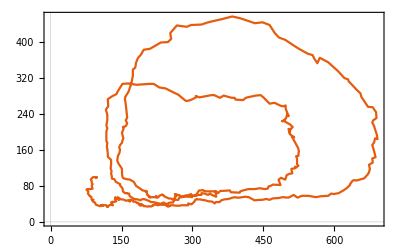
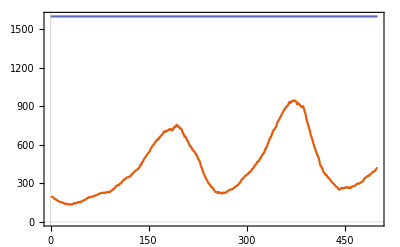

```mathematica
iLatt=20;
countsX=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"];
countsY=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/Y.txt","Table"];
sum=countsX[[;;,2]]+countsY[[;;,2]];
Row[{
ListLinePlot[Transpose[{countsX[[;;,2]],countsY[[;;,2]]}]],
ListLinePlot[{sum,{{0,1600},{500,1600}}},PlotRange->All]
}]
```

```mathematica
iLattStart=1;
iLattEnd=100;
countsX={};
countsY={};
Do[
countsXtmp=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"];
countsYtmp=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/Y.txt","Table"];
If[countsXtmp[[-1,2]]≠0&&countsYtmp[[-1,2]]≠0,
AppendTo[countsX,countsXtmp];
AppendTo[countsY,countsYtmp];
,
Print["Not: "<>ToString[iLatt]];
];
,{iLatt,iLattStart,iLattEnd}];
countsX=Mean[countsX]//N;
countsY=Mean[countsY]//N;
pltData=Transpose[{countsX[[;;,2]],countsY[[;;,2]]}];
```

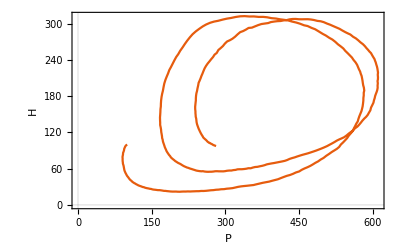

```mathematica
pltMean=ListLinePlot[pltData,FrameLabel->{"P","H"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/mean.pdf",pltMean]
```

figures/mean.pdf

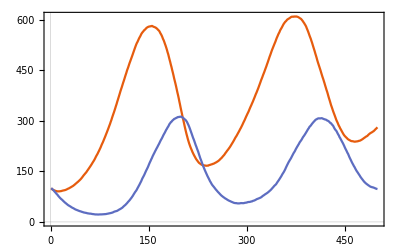

```mathematica
pltMean2=ListLinePlot[Transpose[pltData]]
```

```mathematica
139,349
```

```mathematica
Manipulate[Show[ListPlot[pltData,FrameLabel->{"P","H"}],ListPlot[pltData[[t;;t+1]],PlotStyle->Black],PlotRange->{{500,600},{100,200}}],{t,1,500,1}]
```

```mathematica
fMakePlot[times_,iLatt_]:=Module[{data1,data2,dataX1,dataX2,data11,data22,dataY1,dataY2},
data1=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[times[[1]],10,4]<>".txt","Table"];
data2=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[times[[2]],10,4]<>".txt","Table"];
dataX1=Select[data1,#[[3]]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,#[[3]]=="Y"&][[;;,{1,2}]];
dataX2=Select[data2,#[[3]]=="X"&][[;;,{1,2}]];
dataY2=Select[data2,#[[3]]=="Y"&][[;;,{1,2}]];
data11=ConstantArray[0,{boxLength,boxLength}];
data22=ConstantArray[0,{boxLength,boxLength}];
Do[
data11[[pt[[1]],pt[[2]]]]=1;
,{pt,dataX1}];
Do[
data11[[pt[[1]],pt[[2]]]]=2;
,{pt,dataY1}];
Do[
data22[[pt[[1]],pt[[2]]]]=1;
,{pt,dataX2}];
Do[
data22[[pt[[1]],pt[[2]]]]=2;
,{pt,dataY2}];
Return[Grid[{{
ArrayPlot[data11,ImageSize->400,ColorRules->{0->White,1->Black,2->Blue}],
ArrayPlot[data22,ImageSize->400,ColorRules->{0->White,1->Black,2->Blue}]
}}]]
];
```

```mathematica
times={140,348};
Manipulate[
fMakePlot[times,iLatt]
,{iLatt,1,10,1}]
```

Import::nffil: File data/lattice_v001/lattice/0140.txt not found during Import.

Import::nffil: File data/lattice_v001/lattice/0348.txt not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦3⟧==X&].

Part::partd: Part specification Select[$Failed,#1⟦3⟧==X&]⟦1;;All,{1,2}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦3⟧==Y&].

Part::partd: Part specification Select[$Failed,#1⟦3⟧==Y&]⟦1;;All,{1,2}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦3⟧==X&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::partd: Part specification Select[$Failed,#1⟦3⟧==X&]⟦1;;All,{1,2}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Do::iterb: Iterator {pt,dataX1$9314390} does not have appropriate bounds.

Do::iterb: Iterator {pt,dataY1$9314390} does not have appropriate bounds.

Do::iterb: Iterator {pt,dataX2$9314390} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

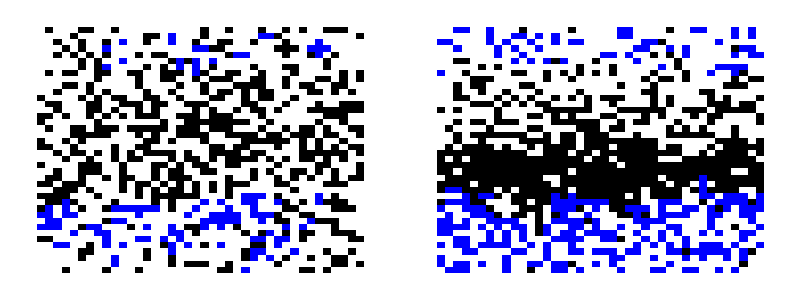

```mathematica
plts=fMakePlot[times,4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/lattices.pdf",plts]
```

figures/lattices.pdf